```mathematica
x=Table[Import[NotebookDirectory[]<>"ticks\\ticks_t5_b10_b0_r"<>ToString@i<>".dat"],{i,51}];
Dimensions@x
xx=Table[Import[NotebookDirectory[]<>"ticks1\\ticks1_t5_b10_b0_r"<>ToString@i<>".dat"],{i,51}];
Dimensions@xx
```

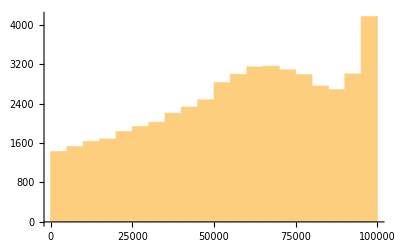

-Graphics-

```mathematica
g1=Histogram[Flatten[x[[All,All,1]]]]
g1x=Histogram[Flatten[xx[[All,All,1]]]]
```

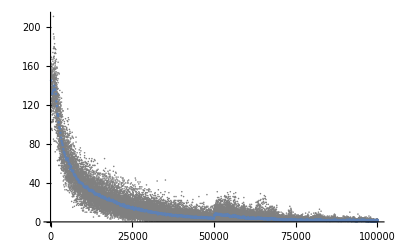

```mathematica
g2=ListPlot[({#[[1]],Total[#[[2;;-1]]]}&/@#)&/@x,Joined->False,PlotRange->All,PlotStyle->Gray];
y=GroupBy[Flatten[({#[[1]],Total[#[[2;;-1]]]}&/@#)&/@x,1],First->Last,Mean];
g3=ListPlot[y,PlotRange->All];
Show@{g2,g3}
```

```mathematica
y=Total[Total[#[[All,2;;-1]]]]&/@x
```

{8408.,10903.,13586.,9767.,8737.,9492.,12697.,9889.,8904.,9823.,10815.,12316.,13054.,12036.,10842.,9677.,7981.,10174.,9536.,10879.,9163.,7686.,8624.,10086.,8847.,7824.,9801.,11917.,6647.,6101.,12261.,12967.,8370.,7179.,10817.,15046.,9991.,5706.,9343.,9788.,10657.,12664.,6956.,10693.,8995.,11329.,10045.,10778.,7534.,10303.,12117.}

```mathematica
Max@y
Mean@y
Min@y
StandardDeviation@y
```

15046.

9995.12

5706.

1985.5

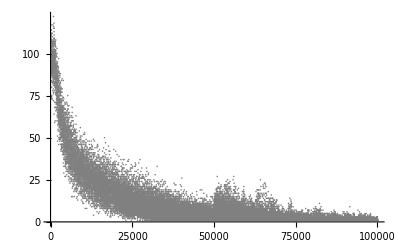

```mathematica
g2=ListPlot[({#[[1]],#[[2]]}&/@#)&/@xx,Joined->False,PlotRange->All,PlotStyle->Gray]
```

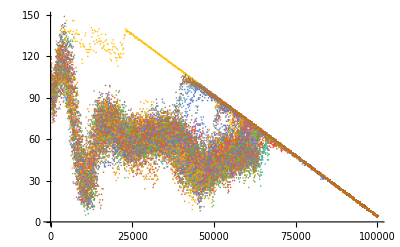

```mathematica
ListPlot[Table[Import[NotebookDirectory[]<>"ticks1\\ticks1_t30_b10_b0_r"<>ToString@i<>".dat"],{i,51}]]
```

```mathematica
x=Table[Import[NotebookDirectory[]<>"ticks1\\ticks1_t30_b10_b0_r"<>ToString@i<>".dat"],{i,51}];
Dimensions@x
```

{51,2163,2}

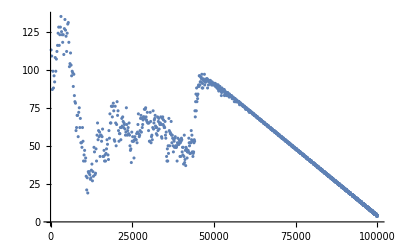

{{48408.,92.},{48503.,93.},{48598.,92.},{48692.,92.},{48786.,92.},{48880.,93.},{48974.,91.},{49068.,92.},{49162.,91.},{49255.,90.},{49348.,91.},{49441.,92.},{49534.,90.},{49627.,91.},{49720.,91.},{49812.,91.},{49904.,90.},{49996.,91.},{50088.,90.},{50180.,91.},{50272.,91.},{50364.,91.},{50455.,89.},{50546.,90.},{50637.,89.},{50728.,89.},{50819.,90.},{50910.,88.},{51000.,88.},{51090.,90.},{51180.,89.},{51270.,90.},{51360.,87.},{51450.,86.},{51539.,88.},{51628.,89.},{51717.,88.},{51806.,89.},{51895.,87.},{51984.,87.},{52073.,86.},{52161.,86.},{52249.,83.},{52337.,85.},{52425.,88.},{52513.,87.},{52601.,86.},{52688.,86.},{52775.,86.},{52862.,86.},{52949.,87.},{53036.,86.},{53123.,87.},{53210.,83.},{53296.,84.},{53382.,86.},{53468.,85.},{53554.,85.},{53640.,85.},{53726.,85.},{53811.,83.},{53896.,84.},{53981.,85.},{54066.,85.},{54151.,85.},{54236.,83.},{54321.,83.},{54405.,83.},{54489.,84.},{54573.,84.},{54657.,82.},{54741.,84.},{54825.,83.},{54909.,83.},{54992.,83.},{55075.,83.},{55158.,83.},{55241.,83.},{55324.,83.},{55407.,82.},{55489.,82.},{55571.,81.},{55653.,82.},{55735.,81.},{55817.,81.},{55899.,82.},{55981.,81.},{56062.,81.},{56143.,81.},{56224.,79.},{56305.,81.},{56386.,81.},{56467.,81.},{56548.,80.},{56628.,79.},{56708.,80.},{56788.,79.},{56868.,80.},{56948.,79.},{57028.,80.},{57108.,79.},{57187.,79.},{57266.,79.},{57345.,79.},{57424.,79.},{57503.,79.},{57582.,79.},{57661.,79.},{57740.,78.},{57818.,77.},{57896.,78.},{57974.,78.},{58052.,78.},{58130.,78.},{58208.,78.},{58286.,77.},{58363.,77.},{58440.,77.},{58517.,77.},{58594.,77.},{58671.,77.},{58748.,77.},{58825.,76.},{58901.,76.},{58977.,76.},{59053.,76.},{59129.,76.},{59205.,76.},{59281.,76.},{59357.,76.},{59433.,75.},{59508.,75.},{59583.,75.},{59658.,74.},{59733.,75.},{59808.,75.},{59883.,75.},{59958.,74.},{60032.,74.},{60106.,74.},{60180.,74.},{60254.,74.},{60328.,74.},{60402.,74.},{60476.,74.},{60550.,73.},{60623.,73.},{60696.,73.},{60769.,72.},{60842.,73.},{60915.,73.},{60988.,73.},{61061.,73.},{61134.,72.},{61206.,72.},{61278.,72.},{61350.,72.},{61422.,72.},{61494.,72.},{61566.,72.},{61638.,72.},{61710.,71.},{61781.,71.},{61852.,71.},{61923.,71.},{61994.,71.},{62065.,71.},{62136.,71.},{62207.,71.},{62278.,70.},{62348.,70.},{62418.,70.},{62488.,70.},{62558.,70.},{62628.,70.},{62698.,70.},{62768.,70.},{62838.,69.},{62907.,69.},{62976.,69.},{63045.,69.},{63114.,69.},{63183.,69.},{63252.,69.},{63321.,69.},{63390.,68.},{63458.,68.},{63526.,68.},{63594.,68.},{63662.,68.},{63730.,68.},{63798.,68.},{63866.,68.},{63934.,67.},{64001.,67.},{64068.,67.},{64135.,67.},{64202.,67.},{64269.,67.},{64336.,67.},{64403.,67.},{64470.,67.},{64537.,66.},{64603.,66.},{64669.,66.},{64735.,66.},{64801.,66.},{64867.,66.},{64933.,66.},{64999.,66.},{65065.,65.},{65130.,65.},{65195.,65.},{65260.,65.},{65325.,65.},{65390.,65.},{65455.,65.},{65520.,65.},{65585.,65.},{65650.,64.},{65714.,64.},{65778.,64.},{65842.,64.},{65906.,64.},{65970.,64.},{66034.,64.},{66098.,64.},{66162.,64.},{66226.,63.},{66289.,63.},{66352.,63.},{66415.,63.},{66478.,63.},{66541.,63.},{66604.,63.},{66667.,63.},{66730.,63.},{66793.,62.},{66855.,62.},{66917.,62.},{66979.,62.},{67041.,62.},{67103.,62.},{67165.,62.},{67227.,62.},{67289.,62.},{67351.,61.},{67412.,61.},{67473.,61.},{67534.,61.},{67595.,61.},{67656.,61.},{67717.,61.},{67778.,61.},{67839.,61.},{67900.,60.},{67960.,60.},{68020.,60.},{68080.,60.},{68140.,60.},{68200.,60.},{68260.,60.},{68320.,60.},{68380.,60.},{68440.,60.},{68500.,59.},{68559.,59.},{68618.,59.},{68677.,59.},{68736.,59.},{68795.,59.},{68854.,59.},{68913.,59.},{68972.,59.},{69031.,59.},{69090.,58.},{69148.,58.},{69206.,58.},{69264.,58.},{69322.,58.},{69380.,58.},{69438.,58.},{69496.,58.},{69554.,58.},{69612.,57.},{69669.,57.},{69726.,57.},{69783.,57.},{69840.,57.},{69897.,57.},{69954.,57.},{70011.,57.},{70068.,57.},{70125.,57.},{70182.,56.},{70238.,56.},{70294.,56.},{70350.,56.},{70406.,56.},{70462.,56.},{70518.,56.},{70574.,56.},{70630.,56.},{70686.,56.},{70742.,55.},{70797.,55.},{70852.,55.},{70907.,55.},{70962.,55.},{71017.,55.},{71072.,55.},{71127.,55.},{71182.,55.},{71237.,55.},{71292.,55.},{71347.,54.},{71401.,54.},{71455.,54.},{71509.,54.},{71563.,54.},{71617.,54.},{71671.,54.},{71725.,54.},{71779.,54.},{71833.,54.},{71887.,53.},{71940.,53.},{71993.,53.},{72046.,53.},{72099.,53.},{72152.,53.},{72205.,53.},{72258.,53.},{72311.,53.},{72364.,53.},{72417.,53.},{72470.,52.},{72522.,52.},{72574.,52.},{72626.,52.},{72678.,52.},{72730.,52.},{72782.,52.},{72834.,52.},{72886.,52.},{72938.,52.},{72990.,52.},{73042.,51.},{73093.,51.},{73144.,51.},{73195.,51.},{73246.,51.},{73297.,51.},{73348.,51.},{73399.,51.},{73450.,51.},{73501.,51.},{73552.,51.},{73603.,50.},{73653.,50.},{73703.,50.},{73753.,50.},{73803.,50.},{73853.,50.},{73903.,50.},{73953.,50.},{74003.,50.},{74053.,50.},{74103.,50.},{74153.,49.},{74202.,49.},{74251.,49.},{74300.,49.},{74349.,49.},{74398.,49.},{74447.,49.},{74496.,49.},{74545.,49.},{74594.,49.},{74643.,49.},{74692.,49.},{74741.,48.},{74789.,48.},{74837.,48.},{74885.,48.},{74933.,48.},{74981.,48.},{75029.,48.},{75077.,48.},{75125.,48.},{75173.,48.},{75221.,48.},{75269.,48.},{75317.,47.},{75364.,47.},{75411.,47.},{75458.,47.},{75505.,47.},{75552.,47.},{75599.,47.},{75646.,47.},{75693.,47.},{75740.,47.},{75787.,47.},{75834.,47.},{75881.,46.},{75927.,46.},{75973.,46.},{76019.,46.},{76065.,46.},{76111.,46.},{76157.,46.},{76203.,46.},{76249.,46.},{76295.,46.},{76341.,46.},{76387.,46.},{76433.,45.},{76478.,45.},{76523.,45.},{76568.,45.},{76613.,45.},{76658.,45.},{76703.,45.},{76748.,45.},{76793.,45.},{76838.,45.},{76883.,45.},{76928.,45.},{76973.,45.},{77018.,44.},{77062.,44.},{77106.,44.},{77150.,44.},{77194.,44.},{77238.,44.},{77282.,44.},{77326.,44.},{77370.,44.},{77414.,44.},{77458.,44.},{77502.,44.},{77546.,44.},{77590.,43.},{77633.,43.},{77676.,43.},{77719.,43.},{77762.,43.},{77805.,43.},{77848.,43.},{77891.,43.},{77934.,43.},{77977.,43.},{78020.,43.},{78063.,43.},{78106.,43.},{78149.,42.},{78191.,42.},{78233.,42.},{78275.,42.},{78317.,42.},{78359.,42.},{78401.,42.},{78443.,42.},{78485.,42.},{78527.,42.},{78569.,42.},{78611.,42.},{78653.,42.},{78695.,41.},{78736.,41.},{78777.,41.},{78818.,41.},{78859.,41.},{78900.,41.},{78941.,41.},{78982.,41.},{79023.,41.},{79064.,41.},{79105.,41.},{79146.,41.},{79187.,41.},{79228.,41.},{79269.,40.},{79309.,40.},{79349.,40.},{79389.,40.},{79429.,40.},{79469.,40.},{79509.,40.},{79549.,40.},{79589.,40.},{79629.,40.},{79669.,40.},{79709.,40.},{79749.,40.},{79789.,40.},{79829.,40.},{79869.,39.},{79908.,39.},{79947.,39.},{79986.,39.},{80025.,39.},{80064.,39.},{80103.,39.},{80142.,39.},{80181.,39.},{80220.,39.},{80259.,39.},{80298.,39.},{80337.,39.},{80376.,39.},{80415.,38.},{80453.,38.},{80491.,38.},{80529.,38.},{80567.,38.},{80605.,38.},{80643.,38.},{80681.,38.},{80719.,38.},{80757.,38.},{80795.,38.},{80833.,38.},{80871.,38.},{80909.,38.},{80947.,38.},{80985.,37.},{81022.,37.},{81059.,37.},{81096.,37.},{81133.,37.},{81170.,37.},{81207.,37.},{81244.,37.},{81281.,37.},{81318.,37.},{81355.,37.},{81392.,37.},{81429.,37.},{81466.,37.},{81503.,37.},{81540.,36.},{81576.,36.},{81612.,36.},{81648.,36.},{81684.,36.},{81720.,36.},{81756.,36.},{81792.,36.},{81828.,36.},{81864.,36.},{81900.,36.},{81936.,36.},{81972.,36.},{82008.,36.},{82044.,36.},{82080.,36.},{82116.,35.},{82151.,35.},{82186.,35.},{82221.,35.},{82256.,35.},{82291.,35.},{82326.,35.},{82361.,35.},{82396.,35.},{82431.,35.},{82466.,35.},{82501.,35.},{82536.,35.},{82571.,35.},{82606.,35.},{82641.,35.},{82676.,34.},{82710.,34.},{82744.,34.},{82778.,34.},{82812.,34.},{82846.,34.},{82880.,34.},{82914.,34.},{82948.,34.},{82982.,34.},{83016.,34.},{83050.,34.},{83084.,34.},{83118.,34.},{83152.,34.},{83186.,34.},{83220.,34.},{83254.,33.},{83287.,33.},{83320.,33.},{83353.,33.},{83386.,33.},{83419.,33.},{83452.,33.},{83485.,33.},{83518.,33.},{83551.,33.},{83584.,33.},{83617.,33.},{83650.,33.},{83683.,33.},{83716.,33.},{83749.,33.},{83782.,33.},{83815.,32.},{83847.,32.},{83879.,32.},{83911.,32.},{83943.,32.},{83975.,32.},{84007.,32.},{84039.,32.},{84071.,32.},{84103.,32.},{84135.,32.},{84167.,32.},{84199.,32.},{84231.,32.},{84263.,32.},{84295.,32.},{84327.,32.},{84359.,32.},{84391.,31.},{84422.,31.},{84453.,31.},{84484.,31.},{84515.,31.},{84546.,31.},{84577.,31.},{84608.,31.},{84639.,31.},{84670.,31.},{84701.,31.},{84732.,31.},{84763.,31.},{84794.,31.},{84825.,31.},{84856.,31.},{84887.,31.},{84918.,31.},{84949.,30.},{84979.,30.},{85009.,30.},{85039.,30.},{85069.,30.},{85099.,30.},{85129.,30.},{85159.,30.},{85189.,30.},{85219.,30.},{85249.,30.},{85279.,30.},{85309.,30.},{85339.,30.},{85369.,30.},{85399.,30.},{85429.,30.},{85459.,30.},{85489.,30.},{85519.,29.},{85548.,29.},{85577.,29.},{85606.,29.},{85635.,29.},{85664.,29.},{85693.,29.},{85722.,29.},{85751.,29.},{85780.,29.},{85809.,29.},{85838.,29.},{85867.,29.},{85896.,29.},{85925.,29.},{85954.,29.},{85983.,29.},{86012.,29.},{86041.,29.},{86070.,29.},{86099.,28.},{86127.,28.},{86155.,28.},{86183.,28.},{86211.,28.},{86239.,28.},{86267.,28.},{86295.,28.},{86323.,28.},{86351.,28.},{86379.,28.},{86407.,28.},{86435.,28.},{86463.,28.},{86491.,28.},{86519.,28.},{86547.,28.},{86575.,28.},{86603.,28.},{86631.,28.},{86659.,27.},{86686.,27.},{86713.,27.},{86740.,27.},{86767.,27.},{86794.,27.},{86821.,27.},{86848.,27.},{86875.,27.},{86902.,27.},{86929.,27.},{86956.,27.},{86983.,27.},{87010.,27.},{87037.,27.},{87064.,27.},{87091.,27.},{87118.,27.},{87145.,27.},{87172.,27.},{87199.,27.},{87226.,26.},{87252.,26.},{87278.,26.},{87304.,26.},{87330.,26.},{87356.,26.},{87382.,26.},{87408.,26.},{87434.,26.},{87460.,26.},{87486.,26.},{87512.,26.},{87538.,26.},{87564.,26.},{87590.,26.},{87616.,26.},{87642.,26.},{87668.,26.},{87694.,26.},{87720.,26.},{87746.,26.},{87772.,26.},{87798.,25.},{87823.,25.},{87848.,25.},{87873.,25.},{87898.,25.},{87923.,25.},{87948.,25.},{87973.,25.},{87998.,25.},{88023.,25.},{88048.,25.},{88073.,25.},{88098.,25.},{88123.,25.},{88148.,25.},{88173.,25.},{88198.,25.},{88223.,25.},{88248.,25.},{88273.,25.},{88298.,25.},{88323.,25.},{88348.,25.},{88373.,24.},{88397.,24.},{88421.,24.},{88445.,24.},{88469.,24.},{88493.,24.},{88517.,24.},{88541.,24.},{88565.,24.},{88589.,24.},{88613.,24.},{88637.,24.},{88661.,24.},{88685.,24.},{88709.,24.},{88733.,24.},{88757.,24.},{88781.,24.},{88805.,24.},{88829.,24.},{88853.,24.},{88877.,24.},{88901.,24.},{88925.,23.},{88948.,23.},{88971.,23.},{88994.,23.},{89017.,23.},{89040.,23.},{89063.,23.},{89086.,23.},{89109.,23.}}

```mathematica
ListPlot[x[[1]]]
x[[1,-1800;;-1000]]
```